```mathematica
Clear["Global`*"];
kHz=10^3;nm=10^-9;mK=10^-3;uK=10^-6;us=10^-6;
um=10^-6;
kB=1.38064852 10^-23;ℏ=1.0545718 10^-34;amu=1.66054 10^-27;
mCs=132.90545 amu;mNa = 23amu;
a0= 5.2917721067 10^-11;
ϵ0=8.854187817 10^-12;
c=299792458;
cm=10^-2;
ms=10^-3;
ωrCs=2π 145kHz;
ωaCs=2π 25kHz;
ωrNa=2π 145kHz;
ωaNa=2π 26kHz;
μ=(mNa mCs)/(mCs+mNa);
Ψ[m_,ω_,n_,x_]:=((m ω)/(π ℏ))^(1/4)1/(√(2^n n!))Exp[-(m ω)/(2 ℏ)x^2]HermiteH[n,√((m ω)/ℏ)x];
```

```mathematica
data=Reap[Do[Sow[{n,√Integrate[x^2 Ψ[mCs,ωrCs,n,x]^2,{x,-Infinity,Infinity}]/nm}
]
,{n,0,10}]][[2,1]];
```

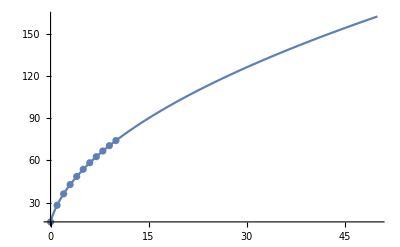

```mathematica
nlm=NonlinearModelFit[data[[;;-2]],a+b √(2 n+1),{a,b},n];
Show[{Plot[nlm[n],{n,0,50}],
ListPlot[data]
}]
```

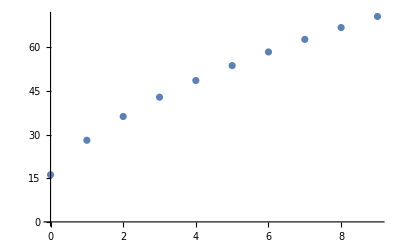

```mathematica
ListPlot[data[[;;-2]]]
```

```mathematica
Solve[nlm[n]==100,n]
```

{{n→18.5662}}

```mathematica
nlm[n]
```

2.43505×10^-10+16.194 √(1+2 n)

```mathematica
√(ℏ/(2 mCs ωrCs))/nm
```

16.194

```mathematica
T=140uK;
nbar=1/(Exp[(ℏ ωrCs)/(kB T)]-1)
```

19.6223